#### Igel1995

```mathematica
CmatIgel=({{10.0, 3.5, 2.5, -5.0, 0.1, 0.3}, {3.5, 8.0, 1.5, 0.2, -0.1, -0.15}, {2.5, 1.5, 6.0, 1.0, 0.4, 0.24}, {-5.0, 0.2, 1.0, 5.0, 0.35, 0.525}, {0.1, -0.1, 0.4, 0.35, 4.0, -1.0}, {0.3, -0.15, 0.24, 0.525, -1.0, 3.0}});
CmatIgel==Transpose[CmatIgel]
TmatIgel = Simplify[TmatOfCmat[CmatIgel]];
MatrixNote[TmatIgel]="Tmat is TmatIgel";
Print["A given Voigt matrix is ",MatrixForm[CmatIgel]];  
Print["The corresponding [T]_𝔹𝔹 is ",MatrixForm[TmatIgel]];
```

#### TmatMar17

```mathematica
TmatPert=({{474, 22, 22, 18, 4, 10}, {22, 374, -22, 28, -16, -34}, {22, -22, 318, 6, -26, 6}, {18, 28, 6, 262, 8, 14}, {4, -16, -26, 8, 32, 42}, {10, -34, 6, 14, 42, 74}});
TmatMar17=MatrixUbar[ZRot[-20.Degree].XRot[-30Degree]].TmatPert.Transpose[MatrixUbar[ZRot[-20Degree].XRot[-30Degree]]];
MatrixNote[TmatMar17]="Tmat is TmatMar17";
```

#### Choose Tmat, then check

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatIgel;
```

```mathematica
MatrixNote[Tmat]
TmatIgel==Transpose[TmatIgel]
MatrixForm[Tmat]
```

## The superlattice

#### Choose one :

```mathematica
WantDetails="WantDetails"
```

```mathematica
WantDetails="NoWantDetails"
```

```mathematica
RangeSigmaAll={TRIV,MONO,ORTH,TET,CUBE,ISO,XISO,TRIG};
```

#### Closest Tmat for each Sigma symmetry class

```mathematica
OutputFor[Tmat,#]&/@RangeSigmaAll;
```

#### Be sure the Nodes all have decimal points. No integers. That is, 4., not 4, and 2., not 2

```mathematica
ww=1;ww=1.2;
Clear[SigmaOfPt];
SigmaOfPt[{x_,y_}]:="";
Node[ISO]:={0.,5-.5};  SigmaOfPt[Node[ISO]]="ISO";
Node[XISO]:={-1ww,4.};SigmaOfPt[Node[XISO]]="XISO";
Node[TRIG]:={-1ww,2.5};SigmaOfPt[Node[TRIG]]="TRIG";
Node[CUBE]:={   1ww,4.};SigmaOfPt[Node[CUBE]]="CUBE";
Node[TET]:={  1ww,3.};SigmaOfPt[Node[TET]]="TET";
Node[ORTH]:={  1ww,2.};SigmaOfPt[Node[ORTH]]="ORTH";
Node[MONO]:={0.,1+.5};SigmaOfPt[Node[MONO]]="MONO";
Node[TRIV]:={0.,0+.5};SigmaOfPt[Node[TRIV]]="TRIV";
dummy;
```

```mathematica
SigmaOfN[n_,path_]:=SigmaOfPt[points[[path[[n]]]]]
```

```mathematica
LatticeBlank:={Arrowheads[.0008],Thickness[.0015],Dashing[{.013,.013}],
{Arrow[{Node[TRIV],Node[MONO]},.25]},  (* from TRIV to MONO *)
{Arrow[{Node[MONO],Node[ORTH]},.25]},  (* from MONO to ORTH *)
{Arrow[{Node[ORTH],Node[TET]},.2]},   (* from ORTH *)
{Arrow[{Node[TET],Node[CUBE]},.2]},   (* from TET to CUBE *)
{Arrow[{Node[TRIG],Node[XISO]},.2]},   (* from TRIG to XISO *)
{Arrow[{Node[TET],Node[XISO]},.3]},,   (* from TET to XISO *)
{Arrow[{Node[TRIG],Node[CUBE]},.3]},   (* from TRIG to CUBE *)
{Arrow[{Node[MONO],Node[TRIG]},.3]},   (* from MONO to TRIG *)
{Arrow[{Node[CUBE],Node[ISO]},.25]},   (* from CUBE to ISO *)
{Arrow[{Node[XISO],Node[ISO]},.25]},  (* from XISO to ISO *)
};
```

#### This definition will change if we want the winding path.

```mathematica
SmatOfPt[Node[TRIV]]=Tmat;
SmatOfPt[Node[MONO]]=Closest[Tmat,MONO];
SmatOfPt[Node[ORTH]]=Closest[Tmat,ORTH];
SmatOfPt[Node[TET]]  =Closest[Tmat,TET];
SmatOfPt[Node[XISO]]=Closest[Tmat,XISO];
SmatOfPt[Node[ISO]]  =Closest[Tmat,ISO];
SmatOfPt[Node[TRIG]]=Closest[Tmat,TRIG];SmatOfPt[Node[CUBE]]=Closest[Tmat,CUBE];
```

#### Specify the discretization increment between symmetry classes

```mathematica
dt=0.5;
```

#### Defining the points and the elastic maps at each point. You can change the interval {t, 0, 1, .5}.

```mathematica
PointsAndSmat:=Union[ Flatten[Table[{
{(1-t)Node[TRIV]+t Node[MONO],(1-t)SmatOfPt[Node[TRIV]]+t SmatOfPt[Node[MONO]]},
{(1-t)Node[MONO]+t Node[ORTH],(1-t)SmatOfPt[Node[MONO]]+t SmatOfPt[Node[ORTH]]},
{(1-t)Node[ORTH]+t Node[TET],  (1-t)SmatOfPt[Node[ORTH]]+t SmatOfPt[Node[TET]]},
{(1-t)Node[TET]  +t Node[XISO],(1-t)SmatOfPt[Node[TET]]  +t SmatOfPt[Node[XISO]]},
{(1-t)Node[TET]  +t Node[CUBE],(1-t)SmatOfPt[Node[TET]]  +t SmatOfPt[Node[CUBE]]},
{(1-t)Node[XISO]+t Node[ISO],  (1-t)SmatOfPt[Node[XISO]]+t SmatOfPt[Node[ISO]]},
{(1-t)Node[MONO]+t Node[TRIG],(1-t)SmatOfPt[Node[MONO]]+t SmatOfPt[Node[TRIG]]},
{(1-t)Node[TRIG]+t Node[XISO],(1-t)SmatOfPt[Node[TRIG]]+t SmatOfPt[Node[XISO]]},
{(1-t)Node[TRIG]+t Node[CUBE],(1-t)SmatOfPt[Node[TRIG]]+t SmatOfPt[Node[CUBE]]},
{(1-t)Node[CUBE]+t Node[ISO],  (1-t)SmatOfPt[Node[CUBE]]+t SmatOfPt[Node[ISO]]}},{t,0,1,dt}],1]];
points=#[[1]]&/@PointsAndSmat;
Length[points]
```

#### Here are the points and their positions in the list

```mathematica
points
Graphics[{LatticeBlank,PointSize[.03],
Point/@points,
Text[Style[Position[points,#],12],#+{.3,0}]&/@points},ImageSize->200]
```

#### Save. This finishes the definition of SmatOfPt

```mathematica
(SmatOfPt[#[[1]]]=#[[2]])&/@PointsAndSmat;  (* SAVE *)
```

#### Example: Point 3 in the lattice (closest XISO)

```mathematica
points[[3]]
MatrixForm[SmatOfPt[points[[3]]]]
```

#### Example: the initial Tmat

```mathematica
MatrixForm[Tmat]
MatrixForm[SmatOfPt[points[[6]]]]
```

#### Any 999s in the 8 - tuples/Degree mean you have not run all OutputFor

```mathematica
βT[Tmat_,Σ_]:=999Degree;   (* This should have been entered in FindSymGroupsForPublic *)
βofPt[{x_,y_},Sigma_]:=βT[SmatOfPt[{x,y}],Sigma];
Beta8tuple[pt_]:=βofPt[pt,#]&/@RangeSigmaAll;
```

```mathematica
RangeSigmaAll
```

```mathematica
Beta8tuple[points[[5]]]/Degree
```

#### Again, any 999s in the 8 - tuples/Degree mean you have not run all OutputFor. When you run the lattice for the first time you will see lots of 999s.

```mathematica
Graphics[{LatticeBlank,PointSize[.015],
Point/@points,
{Red,
Arrow[{points[[12]],Node[#]},.1]&/@RangeSigmaAll},
If[True,Text[Style[Round[Beta8tuple[#]/Degree,.01],13],#,{-1.15,0}]&/@points]},ImageSize->900]
Graphics[{LatticeBlank,PointSize[.03],
Point/@points,
Text[Style[Position[points,#],12],#+{.3,0}]&/@points},ImageSize->200]
```

## Beta curves

```mathematica
PathXISO={6,7,8,12,14,15,16,10,3,5,11};
PathCUBE={6,7,8,12,14,15,16,17,18,13,11};
```

### Examples

```mathematica
points[[6]]
```

```mathematica
PathXISO[[4]]
```

```mathematica
points[[PathXISO[[4]]]]
```

```mathematica
Table[{n,βofPt[points[[PathXISO[[n]]]],ORTH]/Degree},{n,1,Length[PathXISO]}]
```

#### Preliminaries for the main diagram.

```mathematica
BetaPts[Sigma_,PathX_]:={Point/@Table[{n,βofPt[points[[PathX[[n]]]],Sigma]/Degree},{n,1,Length[PathX]}],
                                                            Line[Table[{n,βofPt[points[[PathX[[n]]]],Sigma]/Degree},{n,1,Length[PathX]}]]};
```

```mathematica
hue[MONO]=Black;   BetaText[MONO]="β_MONO";
hue[ORTH]=Purple; BetaText[ORTH]="β_ORTH";
hue[TET]  =Blue;      BetaText[TET]  ="β_TET";
hue[CUBE]=Orange; BetaText[CUBE]="β_CUBE";
hue[XISO]=Green;   BetaText[XISO]="β_XISO";
hue[ISO]  =Red;        BetaText[ISO]   ="β_ISO";
hue[TRIG]=Cyan;     BetaText[TRIG] ="β_TRIG";
dummy;
```

#### Specify the beta curves to be plotted (for initial testing, try {ORTH,ISO} )

```mathematica
RangeΣ={ORTH};
```

```mathematica
RangeΣ={ORTH,ISO};
```

```mathematica
RangeΣ={MONO,ORTH,TET,CUBE,ISO,XISO,TRIG};
```

#### Locates the text on the vertical axis.

```mathematica
yText[PathX_,RangeΣ_]:=Max[βofPt[points[[PathX[[1]]]],#]&/@RangeΣ]/Degree;
yText[PathXISO,RangeΣ]
```

#### The main diagram.

```mathematica
BetaPtsDiagram[PathX_,RangeΣ_]:=Graphics[{PointSize[.017],
{hue[#],BetaPts[#,PathX]}&/@RangeΣ,
Table[Text[Style[PathX[[n]],12],     {n,-.06yText[PathX,RangeΣ]}],{n,1,Length[PathX]}],
Text[Style[SigmaOfN[#,PathX],11],{#,-.12yText[PathX,RangeΣ]}]&/@Range[Length[PathX]],
Text[Style[BetaText[#],{hue[#],15}],  {0,βofPt[points[[PathX[[1]]]],#]/Degree}]&/@RangeΣ},
Axes->True,Ticks->{None,Range[0,50,5]},AxesOrigin->{1,0},TicksStyle->12,AspectRatio->1,ImageSize->500]
```

#### OutputAllPts[Sigma] will give the beta values for the specified Sigma and for all the points.

```mathematica
OutputAllPts[Sigma_]:=OutputFor[SmatOfPt[#],Sigma]&/@points;
```

```mathematica
(*OutputAllPts[ORTH]*)
```

```mathematica
(*OutputAllPts[ISO]*)
```

#### Example: NMinimize error message for TmatMar17 (pathological case)

```mathematica
Ttest=SmatOfPt[points[[11]]];
MatrixForm[Ttest]
OutputFor[Ttest,ORTH]
```

```mathematica
DistToVΣofU[Ttest,UsHat[{6.265341668513891,-3.129228992900632,1.5350976895707746}],ORTH]
```

#### KEY COMMAND : this will execute OutputAllPts for all specified Sigmas

```mathematica
OutputAllPts/@RangeΣ
```

### Show two paths for a single symmetry class

```mathematica
Show[{
BetaPtsDiagram[PathXISO,{XISO}],
BetaPtsDiagram[PathCUBE,{XISO}]}]
Show[{
BetaPtsDiagram[PathXISO, {ORTH}],
BetaPtsDiagram[PathCUBE,{ORTH}]}]
```

### Display all chosen Sigma curves for the path through XISO

```mathematica
BetaPtsDiagram[PathXISO,RangeΣ]
```

### Display all chosen Sigma curves for the path through CUBE

```mathematica
BetaPtsDiagram[PathCUBE,RangeΣ]
```

### Display all chosen Sigma curves for the paths through CUBE and XISO

```mathematica
Show[{
BetaPtsDiagram[PathXISO, RangeΣ],
BetaPtsDiagram[PathCUBE,RangeΣ]}]
```

## For reference

### Path through XISO (TmatMar17)

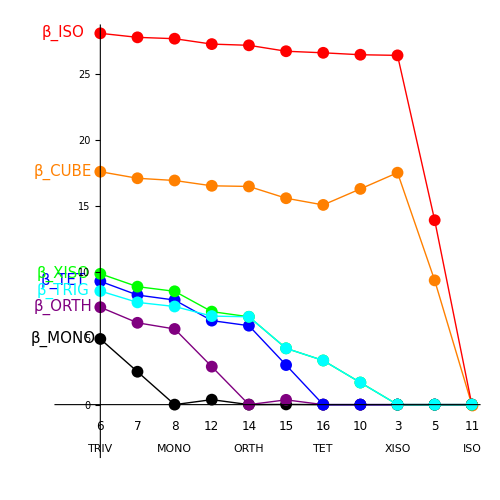

### Path through CUBE (TmatMar17)

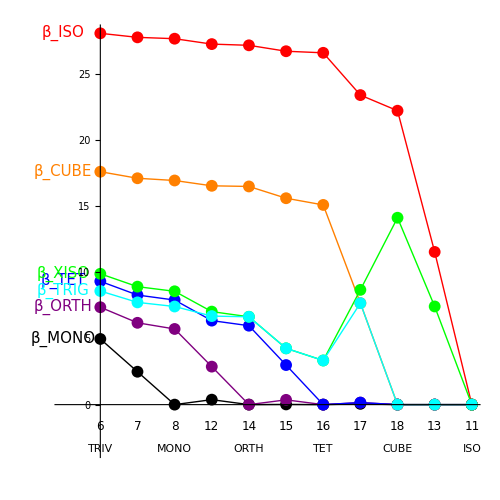

### Paths through XISO and CUBE (TmatMar17)

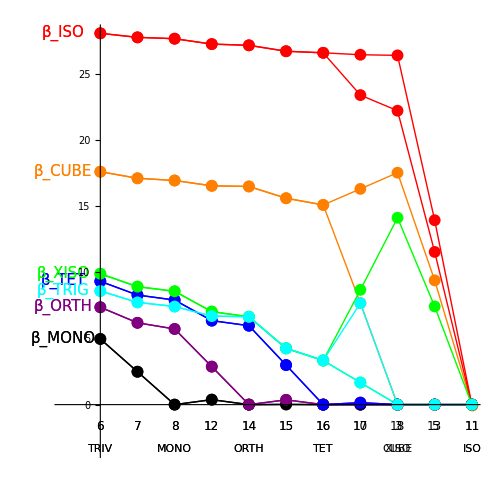

### Path through XISO (Igel)

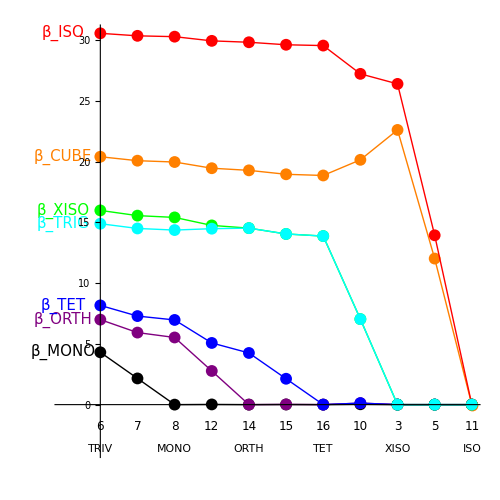

### Path through CUBE (Igel)

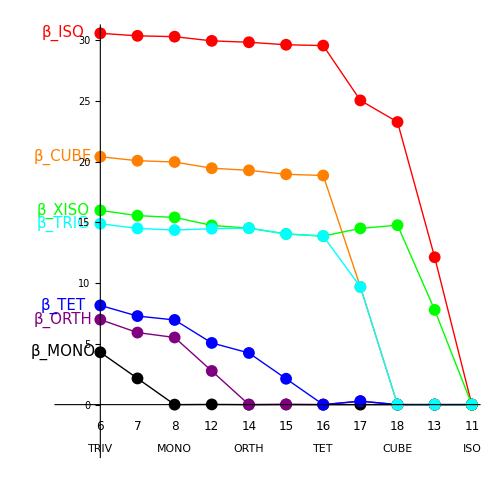

### Paths through XISO and CUBE (Igel)